# The Inverted Pendulum

### Background

This is a brief refresher on some basic Mathematica functionality, centred around an investigation of the inverted pendulum. Have a look at this Youtube video. Your goal is to derive the pendulum’s equation of motion, solve it numerically, and to present the results visually for some different parameter choices.

Let θ denote the angle of the pendulum with respect to the downward direction. The pendulum consists of a massless rod with length l with a mass m attached to the end. Its pivot oscillates vertically with a displacement d[t]=a Sin[ω t]. We will work in units where all lengths are expressed as multiples of l, while time is measured in multiples of 1/ω_0 where ω_0=Sqrt[g/l] is the pendulum’s natural frequency. In these units l=1 and g=1. As seen in the video, for right combination of the pivot’s oscillation amplitude a and frequency ω the point θ=180° will turn into a stable equilibrium point.

```mathematica
ClearAll["Global`*",Derivative]; (*Run if you want to clear all definitions.*)
```

```mathematica
Clear[Derivative];
A = 0.5
M = 2
l = 2
```

0.5

2

2

```mathematica
d[t_, a_] := a * Sin[t]
```

```mathematica
x[t_] := l * Cos[θ[t]]
```

```mathematica
y[t_, a_] := l * Sin[θ[t]] + d[t, a]
```

```mathematica
T[t_, a_, m_] := 1/2 * m *(x'[t]^2 + y'[t,a]^2)
```

```mathematica
V[t_, a_, m_] := m * y[t, a]
```

```mathematica
L[t_, a_, m_] = T[t, a, m] - V[t, a, m]
```

-m (a Sin[t]+2 Sin[θ[t]])+1/2 m (y'[t,a]^2+4 Sin[θ[t]]^2 θ'[t]^2)

```mathematica
-m (a Sin[t]+Sin[θ[t]])+1/2 m (y'[t,a]^2+Sin[θ[t]]^2 θ'[t]^2)
```

### Deriving the EOM

Here I would suggest first defining the x and y coordinates of the pendulum’ s mass as functions of time, in terms of the (undefined) function θ[t]. From this you can define the Lagrange function L as an expression. Using this, derive the equation of motion (remember to use == and not just = here) and assign this to a variable called OEM. Having a ClearAll for the symbols you use in these definitions at the top of the cell will be useful.

```mathematica
EOM = D[L[t, A, M], θ[t]] == D[D[L[t,A,M], θ'[t]]]
```

-4 Cos[θ[t]]+8 Cos[θ[t]] Sin[θ[t]] θ'[t]^2==8 Sin[θ[t]]^2 θ'[t]

```mathematica
solution = NDSolve[{EOM, θ[0] =}]
```

### Drawing the pendulum

Write a function which draws the pendulum for given values of θ, d and l. You can use Graphics for this. You just provide it with a list of objects to draw together with properties (Black, Red, Thick, Thin...). After that you can tune the plot range and aspect ratio. See the example below.

```mathematica
drawfigure[t_]:=Graphics[{Orange,Disk[{0,0},1],Black,Thin,Circle[{0,0},4],Blue,Disk[{4 Cos[t],4 Sin[t]},1/3],Thin,Black,Circle[{4 Cos[t],4 Sin[t]},0.75],Gray,Disk[{4 Cos[t],4 Sin[t]}+{Cos[12 t],Sin[12t]} 0.75,1/9]},PlotRange->{{-5,5},{-5,5}},ImageSize->250];
```

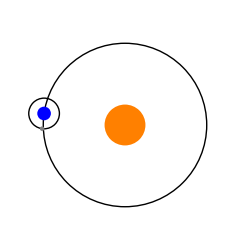

```mathematica
drawfigure[3]
```

```mathematica
Manipulate[drawfigure[t],{t,0,2π,0.005,Appearance->"Open",AnimationRate->80,AnimationRunning->True}]
```

```mathematica
drawPendulum[t_] :=Graphics[{Orange,Disk[{0,d[t]},1]},PlotRange->{{-5,5},{-5,5}},ImageSize->250];
```

```mathematica
drawPendulum[3]
```

-Graphics-

```mathematica
Manipulate[drawPendulum[t],{t,0,2π,0.005,Appearance->"Open",AnimationRate->80,AnimationRunning->True}]
```

### Solving the EOM and visualising the solution

Write code which assigns numeric values to a, ω and θ0=θ(0). Combine this with the code below for solving the EOM, with the pendulum starting from rest. This will assign the solution of the EOM to a function θ. You can plot θ as a function of time, and also use it to produce an animation of the pendulum when combined with the function you defined above. You can put the two plots next to each other using Row.

```mathematica
ClearAll[t,θ,Derivative];
NDSolve[{EOM,θ[0]==θ0,θ'[0]==0},θ,{t,0,500}];
θ=θ/.%[[1]];
```

Depending on the values of a and ω the pendulum can exhibit a wide range of different behaviours. When a is not much smaller than l=1 the motion can be quite chaotic. Here we will take a=0.1. If your code above works then you can just copy and paste the cell and adjust the values of the parameters for the questions below. For this purpose using something like ParametricNDSolve would be better, but this function apparently contains some exciting bugs, so we will stick to a less elegant but more reliable approach here.

### Slow driving

Take ω=3 here and start the pendulum close to the top, say at 175°. Here you can already get an idea of how complicated the motion can be, with periods of back-and-forth swinging, and swinging around clockwise or anti-clockwise all being present in the dynamics.

### Fast driving

A careful analysis of the EOM shows that once (aω)/(lω_0)>Sqrt[2] the pendulum’s top position at θ=180° becomes a stable equilibrium point. (This is still for the case where a<<l=1.) Starting out the pendulum close to this point should therefore lead to stable oscillations around it, provided that the driving is sufficiently fast. Produce an example of this.